# String byte count

### The string “mμ” has two characters and 3 bytes

```mathematica
Length@ToCharacterCode["mμ","UTF-8"]
```

3

```mathematica
Length[StringToByteArray["mμ"]]
```

3

```mathematica
ByteCount["mμ"]
```

56

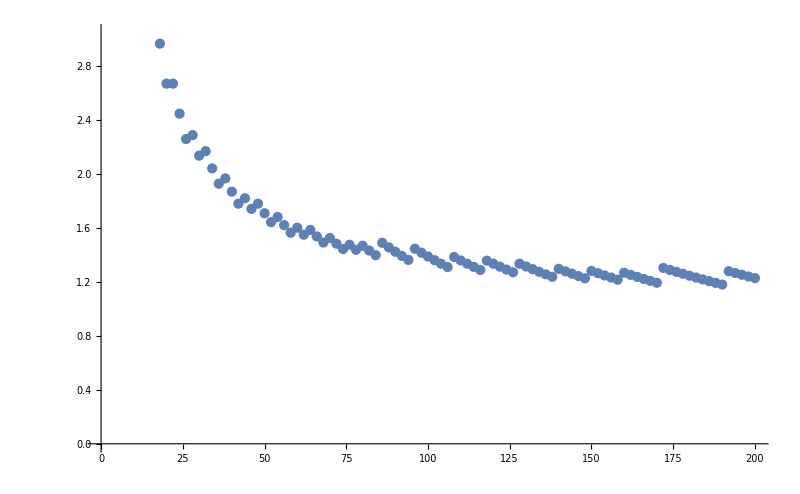

```mathematica
ListPlot[
Table[With[{str=StringRepeat["mμ",len]},{StringLength[str],ByteCount[str]/Length@ToCharacterCode[str,"UTF-8"]}],{len,100}],
ImageSize-> 800
]
```